```mathematica
graphdata={{{0,0},{0.6,0},{0.6,-0.1},{0,-0.1}},{{-0.2,-0.3},{0.8,-0.3},{0.8,-0.41},{-0.2,-0.41}}}
```

{{{0,0},{0.6,0},{0.6,-0.1},{0,-0.1}},{{-0.2,-0.3},{0.8,-0.3},{0.8,-0.41},{-0.2,-0.41}}}

```mathematica
graphdata2={{{0,0},{0.3,0},{0.3,-0.08},{0,-0.08}},{{-0.1,-0.3+0.1},{0.4,-0.3+0.1},{0.4,-0.41+0.12},{-0.1,-0.41+0.12}}}
```

{{{0,0},{0.3,0},{0.3,-0.08},{0,-0.08}},{{-0.1,-0.2},{0.4,-0.2},{0.4,-0.29},{-0.1,-0.29}}}

```mathematica
line1={{0,-0.05},{0.6,-0.05},{-0.2,-(0.3+0.41)/2},{0.8,-(0.3+0.41)/2}}
line2={{0,-0.04},{0.3,-0.04},{-0.1,-(0.2+0.29)/2},{0.4,-(0.2+0.29)/2}}
```

{{0,-0.05},{0.6,-0.05},{-0.2,-0.355},{0.8,-0.355}}

{{0,-0.04},{0.3,-0.04},{-0.1,-0.245},{0.4,-0.245}}

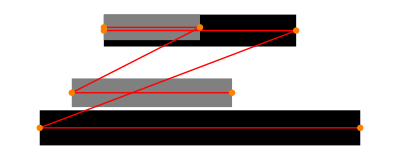

```mathematica
Graphics[{Polygon/@graphdata,Gray,Polygon/@graphdata2,Red,Line@line1,Line@line2,Orange,Disk[#,0.01]&/@line1,Disk[#,0.01]&/@line2}]
```

```mathematica
reducedPoints1=Map[(#-line1⟦1⟧)&,graphdata,{2}];
reducedPoints1=Flatten[reducedPoints1,1]
reducedPoints2=Map[(#-line2⟦1⟧)&,graphdata2,{2}];
reducedPoints2=Flatten[reducedPoints2,1]
```

{{0,0.05},{0.6,0.05},{0.6,-0.05},{0,-0.05},{-0.2,-0.25},{0.8,-0.25},{0.8,-0.36},{-0.2,-0.36}}

{{0,0.04},{0.3,0.04},{0.3,-0.04},{0,-0.04},{-0.1,-0.16},{0.4,-0.16},{0.4,-0.25},{-0.1,-0.25}}

```mathematica
T.{Flatten[line1]}ᵀ==reducedPoints1⟦1⟧
T.{Flatten[line2]}ᵀ==reducedPoints2⟦1⟧
```

T.{{0},{-0.05},{0.6},{-0.05},{-0.2},{-0.355},{0.8},{-0.355}}=={0,0.05}

T.{{0},{-0.04},{0.3},{-0.04},{-0.1},{-0.245},{0.4},{-0.245}}=={0,0.04}

```mathematica
{Flatten[line1],Flatten[line2]}ᵀ
```

{{0,0},{-0.05,-0.04},{0.6,0.3},{-0.05,-0.04},{-0.2,-0.1},{-0.355,-0.245},{0.8,0.4},{-0.355,-0.245}}

```mathematica
NSolve[{T.{Flatten[line1]}ᵀ==reducedPoints1⟦1⟧,T.{Flatten[line2]}ᵀ==reducedPoints2⟦1⟧},T]
```

{}

```mathematica
(Ttest={reducedPoints1⟦1⟧,reducedPoints2⟦1⟧}ᵀ.PseudoInverse[{Flatten[line1],Flatten[line2]}ᵀ])//MatrixForm
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1.6847×10^-16 | -0.024257 | -0.0158581 | -0.024257 | 0.00528603 | -0.105721 | -0.0211441 | -0.105721)

```mathematica
TList=Table[{reducedPoints1⟦i⟧,reducedPoints2⟦i⟧}ᵀ.PseudoInverse[{Flatten[line1],Flatten[line2]}ᵀ],{i,1,Length[Flatten[line1]]}];
```

```mathematica
line1
```

{{0,-0.05},{0.6,-0.05},{-0.2,-0.355},{0.8,-0.355}}

```mathematica
reformed1=Flatten[#.({Flatten[line1]}ᵀ)]&/@TList
reformed2=Flatten[#.({Flatten[line2]}ᵀ)]&/@TList
```

{{0.,0.05},{0.6,0.05},{0.6,-0.05},{0.,-0.05},{-0.2,-0.25},{0.8,-0.25},{0.8,-0.36},{-0.2,-0.36}}

{{0.,0.04},{0.3,0.04},{0.3,-0.04},{0.,-0.04},{-0.1,-0.16},{0.4,-0.16},{0.4,-0.25},{-0.1,-0.25}}

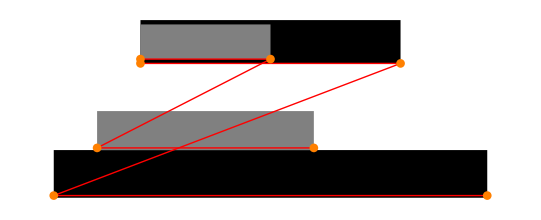

```mathematica
Graphics[{Polygon/@Partition[reformed1,4],Gray,Polygon/@Partition[reformed2,4],Red,Line@line1,Line@line2,Orange,Disk[#,0.01]&/@line1,Disk[#,0.01]&/@line2}]
```

```mathematica
{Flatten[line1],Flatten[line2]}ᵀ//MatrixForm
{reducedPoints1⟦1⟧,reducedPoints2⟦1⟧}ᵀ//MatrixForm
```

(0 | 0
-0.05 | -0.04
0.6 | 0.3
-0.05 | -0.04
-0.2 | -0.1
-0.355 | -0.245
0.8 | 0.4
-0.355 | -0.245)

(0 | 0
0.05 | 0.04)

```mathematica
({{a,b},{c,d}}.line1ᵀ)
```

{{-0.05 b,0.6 a-0.05 b,-0.2 a-0.355 b,0.8 a-0.355 b},{-0.05 d,0.6 c-0.05 d,-0.2 c-0.355 d,0.8 c-0.355 d}}

```mathematica
{{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]},{Subscript[x, 3],Subscript[y, 3]},{Subscript[x, 4],Subscript[y, 4]}}//TraditionalForm
```

(x_1 | y_1
x_2 | y_2
x_3 | y_3
x_4 | y_4)

```mathematica
{{Subscript[ξ, i],Subscript[η, i]}}ᵀ==Subscript[T, i].{Flatten[{{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]},{Subscript[x, 3],Subscript[y, 3]},{Subscript[x, 4],Subscript[y, 4]}}]}ᵀ//TraditionalForm
```

(ξ_i
η_i)==T_i.(x_1
y_1
x_2
y_2
x_3
y_3
x_4
y_4)

```mathematica
x={{1,2,3},{4,5,6}};
xI=PseudoInverse[x]
```

{{-17/18,4/9},{-1/9,1/9},{13/18,-2/9}}

```mathematica
x.xI
```

{{1,0},{0,1}}

```mathematica
(a.b)ᵀ
```

Transpose[a.b]